```mathematica
ψn=1/(√(2^n n!))ⅇ^(-(π x^2)/2)HermiteH[n,√π x](*with mω/πℏ=1*)
```

(ⅇ^(-(π x^2)/2) HermiteH[n,√π x])/(√(2^n n!))

### coherent state

Superposition of Fock states (number states) which approximates a classical oscillator. This is, e.g., what a laser does, in with the electric field taking the place of the position operator.

```mathematica
α=3;
α^n/(√(n!))/.n->30//N
```

0.0126418

```mathematica
ψ=Sum[ψn α^n/(√(n!))ⅇ^(-ⅈ (n+1/2) t),{n,0,30}];
```

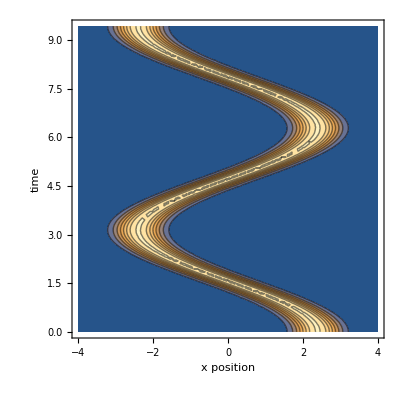

```mathematica
ContourPlot[Abs[ψ]^2,{x,-4,4},{t,0,3π},FrameLabel->{"x position","time"},PlotRange->All]
```

What does the time average of the position of the coherent state look like?

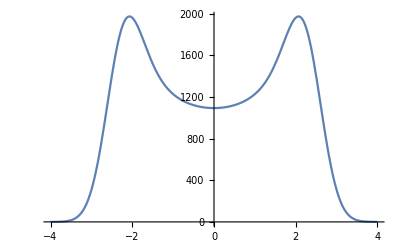

```mathematica
tmax=3π;
Plot[NIntegrate[Abs[ψ]^2,{t,0,tmax}]/tmax,{x,-4,4}]
```

### thermal state

```mathematica
Tfractional=0.1;(*the energy of the oscillator state as a fraction of the potential depth*)
ψ=Sum[ψn Exp[-n Tfractional] ⅇ^(ⅈ n t),{n,0,23}];
```

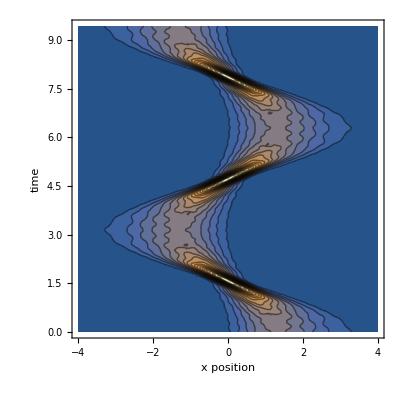

```mathematica
ContourPlot[Abs[ψ]^2,{x,-4,4},{t,0,3π},FrameLabel->{"x position","time"},PlotRange->All,Contours->20]
```

What does the time average of the position of the thermal state look like?

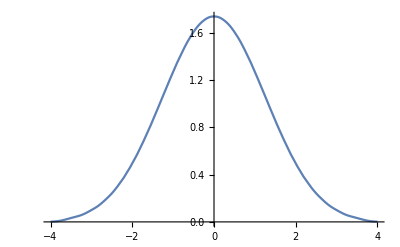

```mathematica
tmax=3π;
Plot[NIntegrate[Abs[ψ]^2,{t,0,tmax}]/tmax,{x,-4,4}]
```

An individual atom will have a sinusoidal trajectory in the trap, but the distribution of the ensemble will still be a thermal state. Try to show this.

The starting position should be dependent on the thermal distribution of the atom, since the trap frequencies don’t depend on the energy of the atom. Is there any other way that initial thermal state effects the atom dynamics?

not correct:

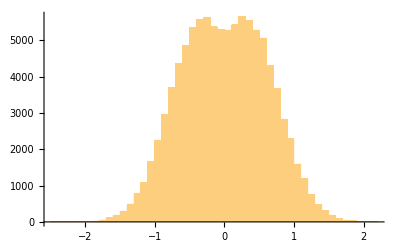

```mathematica
x0=Array[RandomVariate[MaxwellDistribution[0.5]]&,10^5];
Histogram[ x0 Sin[2π RandomReal[{0,1},10^5]],50]
```

{-0.0581954,0.791852,-0.395158,-0.517946,-0.18175,-1.28245,-1.25954,-0.0644562,9984,0.296186,-0.891368,-0.170244,-0.437057,0.0781698,0.975768,-1.93726,-1.00542}
 |  |  |  |

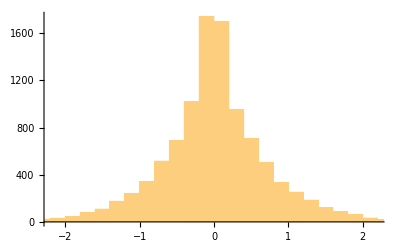

```mathematica
x0=RandomVariate[NormalDistribution[0,1],10^4]
Histogram[ x0 Sin[2π RandomReal[{0,1},10^4]],50]
```

```mathematica
Range[4]Range[4]
```

{1,4,9,16}